# ESSENTIAL CALCULUS SECOND EDITION JAMES STEWART

## CHAPTER 1 FUNCTIONS AND LIMITS

1.5 CONTINUITY

## THEOREM 6

### -Graphics-

## EXAMPLE 6

### -Graphics-

```mathematica
f:=x^100+2 x^37+75
Plot[f,{x,-5,5}]
```

-Graphics-

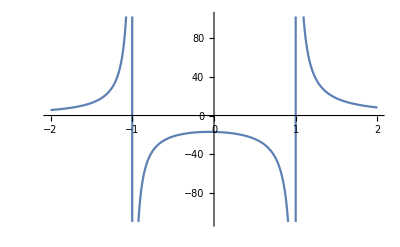

```mathematica
g:=(x^2+2x+17)/(x^2-1)
Plot[g,{x,-2,2}]
```

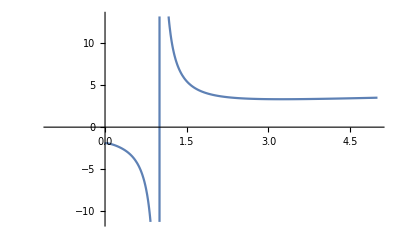

```mathematica
h:=√x+(x+1)/(x-1)-(x+1)/(x^2+1)
Plot[h,{x,-1,5}]
```

## THEOREM 7

### -Graphics- -Graphics-

## THEOREM 8

### -Graphics-

## EXAMPLE 7

### -Graphics-

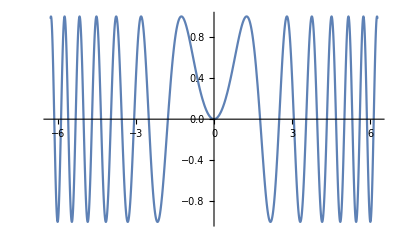

```mathematica
h:=Sin[x^2]
Plot[h,{x,-2π,2π}]
```

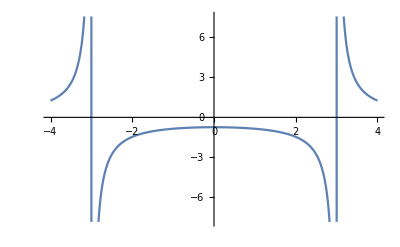

```mathematica
F:=1/(√(x^2+7)-4)
Plot[F,{x,-4,4}]
```

## THEOREM 9: THE INTERMEDIATE VALUE THEOREM

### -Graphics- -Graphics-

## EXAMPLE 8

### -Graphics-

```mathematica
Clear[f]
f[x_]:=4 x^3-6 x^2+3x-2
Plot[f[x],{x,-1,2}]
f[1]
f[2]
Clear[x]
Solve[4 x^3-6 x^2+3x-2==0,x]
N[%]
```

{{x→1.22112},{x→0.139438+0.624512 ⅈ},{x→0.139438-0.624512 ⅈ}}

1.6 LIMITS INVOLVING INFINITY

## INFINITE LIMITS

```mathematica
f[x_]:=1/x^2
Plot[f[x],{x,-5,5}]
Limit[f[x],x->0]
```

∞

### -Graphics-

### DEFINITION 1

#### -Graphics-

### DEFINITION 2

#### -Graphics-

### EXAMPLE 1

#### -Graphics-

```mathematica
f[x_]=(2x)/(x-3)
Plot[f[x],{x,-1,4}]
Limit[f[x],x->3,Direction->1]
Limit[f[x],x->3,Direction->-1]
```

∞

### EXAMPLE 2

#### -Graphics-

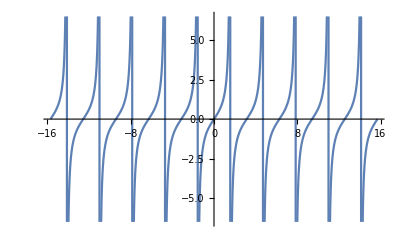

```mathematica
f[x_]=Tan[x]
Plot[f[x],{x,-5π,5π}]
```

## LIMITS AT INFINITY

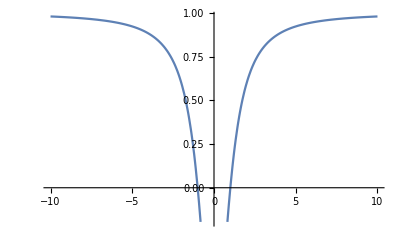

```mathematica
f[x_]:=(x^2-1)/(x^2+1)
Plot[f[x],{x,-10,10}]
```

### DEFINITION 3

#### -Graphics-

### DEFINITION 4

#### -Graphics-

### EXAMPLE 3

Vertical asymptotes

Horizontal asymptotes

### EXAMPLE 4

#### -Graphics-

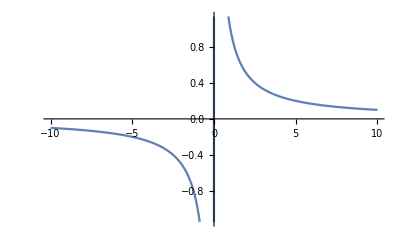

```mathematica
f[x_]:=1/x
Plot[f[x],{x,-10,10}]
```

### 5 RULE

#### -Graphics-

### EXAMPLE 5

#### -Graphics-

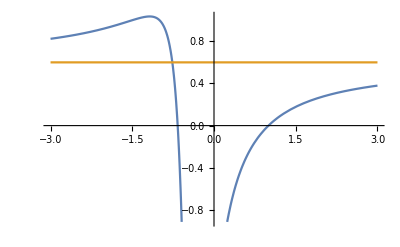

```mathematica
Clear[f]
Clear[g]
f[x_]=(3 x^2-x-2)/(5 x^2+4x+1);
g[x_]=0.6
Plot[{f[x],g[x]},{x,-3,3}]
```

### EXAMPLE 6

#### -Graphics-

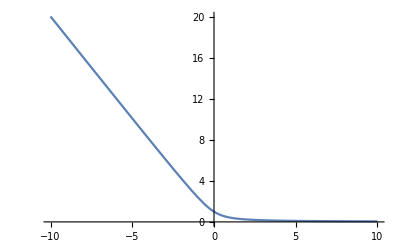

```mathematica
Clear[f]
f[x_]=√(x^2+1)-x
Plot[f[x],{x,-10,10}]
```

### EXAMPLE 7

#### -Graphics-

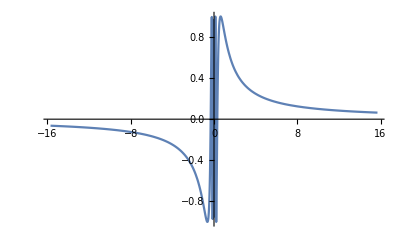

```mathematica
Clear[f]
f[x_]=Sin[1/x]
Plot[f[x],{x,-5π,5π}]
```

### EXAMPLE 8

#### -Graphics-

## INFINITE LIMITS AT INFINITY

### -Graphics-

### EXAMPLE 9

#### -Graphics-

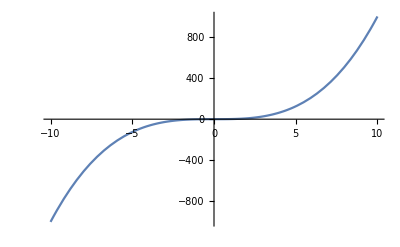

```mathematica
Clear[f]
f[x_]=x^3
Plot[f[x],{x,-10,10}]
```

### EXAMPLE 10

#### -Graphics-

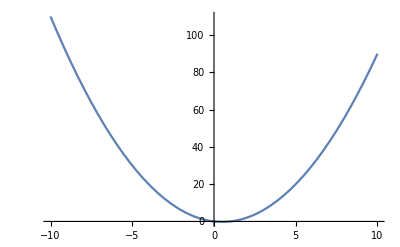

```mathematica
Clear[f]
f[x_]=x^2-x
Plot[f[x],{x,-10,10}]
```

### EXAMPLE 11

#### -Graphics-

```mathematica
Clear[f]
f[x_]=(x^2+x)/(3-x)
Plot[f[x],{x,-10,10}]
```

## PRECISE DEFINITIONS

### DEFINITION 6

#### -Graphics-

#### -Graphics-

#### -Graphics-

### EXAMPLE 12

#### -Graphics-

#### -Graphics-

### DEFINITION 7

#### -Graphics-

#### -Graphics-

#### -Graphics-

#### -Graphics-

### EXAMPLE 13

#### -Graphics-

#### -Graphics-

```mathematica
Clear[f]
f[x_]:=1/x
Plot[f[x],{x,-5,10}]
```

### DEFINITION 8

#### -Graphics-

#### -Graphics-

## CHAPTER 2 DERIVATIVES

2.1 DERIVATIVES AND RATES OF CHANGE

## THE TANGENT PROBLEM

### -Graphics-

### EXAMPLE 1

#### -Graphics-

#### -Graphics-

```mathematica
tg[f_,x_,p_]:=(f'[x]/.x->p) (x-p)+f[p]
q=#^2&;
Manipulate[Plot[{q[x],tg[q,u,m]/.u->x},{x,-3,3},PlotRange->{-5,5},Epilog->{Red,PointSize[0.02],Point[{m,q[m]}]}],{m,-1,1,0.01}]
```

```mathematica
Manipulate[
Switch[ω[x],
x^2,
a=0;b=8;c=2;d=.00001;e=3;f={0,7};g={0,35};h=Max[Min[e,h],d];i={0,-2.5};j={-2,1};k={1,30};l={1,25};m={1,20};n=Text@Style[Row[{"tangent to ",TraditionalForm[y==x^2]," at Q = (2, 4)"}],18],
√x,
a=0;b=20;c=2;d=.00001;e=15;f={0,20};g={0,5};h=Max[Min[e,h],d];i={0,-2.5};j={-1,2};k={7.5,2};l={7.5,1.5};m={7.5,1};n=Text@Style[Row[{"tangent to ",TraditionalForm[y==Sqrt[x]]," at Q = (2, √2)"}],18],
ⅇ^-x,
a=-6;b=6;c=0;d=-2.25;e=4.75;f={-5,5};g={-2,10};h=Max[Min[e,h],d];i={1.5,.5};j={-2,-.75};k={.55,8};l={.55,6};m={.55,4};n=Text@Style[Row[{"tangent to ",TraditionalForm[y==Exp[-x]]," at Q = (0, 1)"}],18]];
Show[
Plot[{ω[x],ω'[c](x-c)+ω[c],(ω[c+h]-ω[c])/h(x-c)+ω[c]},{x,a,b},PlotStyle->{Thick,Red,Brown},PlotLabel->n],
Graphics[{{Thickness->.01,RGBColor[.6,.73,.36],Line[{{c,0},{c+h,0}}]},
PointSize->Large,
Point[{c,ω[c]}],
Text[Style["Q",18],{c,ω[c]},i],
Point[{c+h,ω[c+h]}],
Text[Style["P",18],{c+h,ω[c+h]}, j],
Text[Style[Row[{Style["P"]," = ("<>ToString[c+h]<>", "<>ToString[N[ω[c+h]]]<>")"}],18,Bold],k,{-1,0}],
Text[Style[Row[{Style["h",Italic]," = "<>ToString[h]}],18,Bold,RGBColor[.6,.73,.36]],l,{-1,0}] ,
Text[Style["secant slope = "<>ToString[N[(ω[c+h]-ω[c])/h]],18,Bold,Brown],m ,{-1,0}],
Text[Style[If[h<0,Style["-h",Italic],Style["h",Italic]],RGBColor[.6,.73,.36],20],{c+1/2h,0},{0,-1}]
}],
PlotRange->{f,g},
ImageSize->{535,400}
],
{{ω,#^2&,"y = "},
{#^2&->x^2,√#&->√x,ⅇ^-#&->ⅇ^-x},SetterBar},
{e,3,15,ControlType->None},
{d,-2.25,.00001,ControlType->None},
{{h,e},d,e},
AutorunSequencing->{{4,5}},TrackedSymbols->True
]
```

#### -Graphics-

### DEFINITION 1

#### -Graphics-

#### -Graphics-

### DEFINITION 2

#### -Graphics-

#### -Graphics-

### EXAMPLE 2

#### -Graphics-

#### -Graphics-

```mathematica
Clear[f]
f[x_]:=3/x
Limit[(f[3+h]-f[3])/h,h->0]
```

-1/3

## THE VELOCITY PROBLEM

### -Graphics-

### -Graphics--Graphics-

### DEFINITION 3

#### -Graphics--Graphics-

### EXAMPLE 3

#### -Graphics-

## DERIVATIVES

### DEFINITION 4

#### -Graphics-

### DEFINITION 5

#### -Graphics-

#### -Graphics-

#### -Graphics-

### EXAMPLE 4

#### -Graphics-

```mathematica
tg[f_,x_,p_]:=(f'[x]/.x->p) (x-p)+f[p]
q=(#^2-8#+9)&;
Manipulate[Plot[{q[x],tg[q,u,m]/.u->x},{x,0,8},PlotRange->{-10,12},Epilog->{Red,PointSize[0.02],Point[{m,q[m]}]}],{m,0,8,0.01}]
```

### EXAMPLE 5

#### -Graphics-

## RATE OF CHANGE

### Average rate of change of y with respect to x over the interal [x1,x2]

#### -Graphics-

#### -Graphics-

### Instantaneous rate of change of y with respect to x at x=x1

#### -Graphics-

#### -Graphics-

#### -Graphics--Graphics-

### EXAMPLE 6

#### The rate of change of the debt with respect to time in Example 6 is just one example of a rate of change. Here are a few of the many others: The velocity of a particle is the rate of change of displacement with respect to time. Physicists are interested in other rates of change as well—for instance, the rate of change of work with respect to time (which is called power). Chemists who study a chemical reaction are interested in the rate of change in the concentration of a reactant with respect to time (called the rate of reaction). A steel manufacturer is interested in the rate of change of the cost of producing X tons of steel per day with respect to X (called the marginal cost). A biologist is interested in the rate of change of the population of a colony of bacteria with respect to time. In fact, the computation of rates of change is important in all of the natural sciences, in engineering, and even in the social sciences. All these rates of change can be interpreted as slopes of tangents. This gives added significance to the solution of the tangent problem. Whenever we solve a problem involving tangent lines, we are not just solving a problem in geometry. We are also implicitly solving a great variety of problems involving rates of change in science and engineering.

2.2 THE DERIVATIVE AS A FUNCTION

### EQUATION 1

#### -Graphics-

### EQUATION 2 (from a fixed number a to a variable)

#### -Graphics-

### Example 1

#### -Graphics-

#### -Graphics-

#### -Graphics-

### Example 2

#### -Graphics-

```mathematica
Clear[f]
Clear[x]
f[x_]:=x^3-x
Limit[(f[x+h]-f[x])/h,h->0]
```

```mathematica
Plot[-1+3 x^2,{x,-2,2}]
```

```mathematica
Plot[f[x],{x,-2,2}]
```

### Example 3

#### -Graphics-

```mathematica
Clear[f]
Clear[x]
f[x_]:=√x
Limit[(f[x+h]-f[x])/h,h->0]
```

```mathematica
Plot[1/(2 √x),{x,-3.64,3.64}]
```

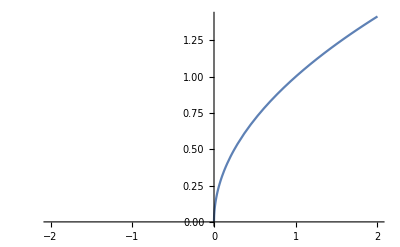

```mathematica
Plot[f[x],{x,-2,2}]
```

#### -Graphics-

### Example 4

#### -Graphics-

```mathematica
Clear[f]
Clear[x]
f[x_]:=(1-x)/(2+x)
Limit[(f[x+h]-f[x])/h,h->0]
```

```mathematica
Plot[-3/(2+x)^2,PlotRange->{{-10,10},{0,-6}}]
```

```mathematica
Plot[-3/(2+x)^2,PlotRange->{{-5,5},{0,-6}},{x,-6,20}]
```

```mathematica
Plot[-3/(2+x)^2,{x,-5,5},PlotRange->{0,-6}]
```

```mathematica
Plot[f[x],{x,-10,10},PlotRange->{-10,10}]
```

## OTHER NOTATIONS

#### -Graphics-

#### -Graphics-

#### -Graphics-

#### -Graphics-

## DIFFERENTIABLE FUNCTIONS

### DEFINITION 3

#### -Graphics-

### EXAMPLE 5

#### -Graphics-

```mathematica
Clear[x]
Clear[f]
f[x_]:=Abs[x]
```

```mathematica
Plot[f[x],{x,-1,1}]
```

```mathematica
FullSimplify[Abs'[x],x∈Reals]
```

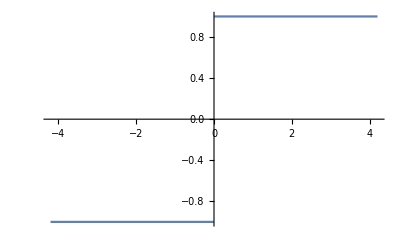

```mathematica
Plot[Sign[x],{x,-4.2,4.2}]
```

#### -Graphics-

### THEOREM 4

#### -Graphics-

#### -Graphics-

#### -Graphics-

## HOW CAN A FUNCTION FAIL TO BE DIFFERENTIABLE

#### In general, if the graph of a function has a “corner” or “kink” in it, then the graph of f has no tangent at this point and is not differentiable there. -Graphics-

#### Theorem 4 gives another way for a function not to have a derivative. It says that if f is not continuous at a, then f is not differentiable at a. So at any discontinuity (for instance, a jump discontinuity) fails to be differentiable. -Graphics-

#### -Graphics- -Graphics--Graphics-

#### A graphing calculator or computer provides another way of looking at differentiability. If f is differentiable at (a, f(a)), then when we zoom in toward the point the graph straightens out and appears more and more like a line. -Graphics-

## HIGHER DERIVATIVES

#### -Graphics-

### EXAMPLE 7

#### -Graphics-

```mathematica
Clear[x]
Clear[f]
f[x_]:=x^3-x
```

```mathematica
Plot[{f[x],f'[x],f''[x]},{x,-1.5,1.5}]
```

### -Graphics- -Graphics-

### EXAMPLE 7

#### -Graphics-

2.3 BASIC DIFFERENTIATION FORMULAS

### DERIVATIVE OF A CONSTANT FUNCTION

#### -Graphics-

#### -Graphics--Graphics-

## POWER FUNCTIONS

#### -Graphics-

#### -Graphics- -Graphics-

### Example 1

#### -Graphics-

#### The power rule is true for all real numbers n.

### THE POWER RULE (GENERAL VERSION)

#### -Graphics-

### Example 2

#### -Graphics-

### Example 3

#### -Graphics-

```mathematica
Clear[y]
Clear[x]
y[x_]:=x √x
yp[x_]:=y'[x]
```

```mathematica
yp[1]
```

```mathematica
TL[x_]:=3/2 x-1/2;
```

```mathematica
NL[x_]:=-2/3 x+5/3;
```

```mathematica
Plot[{y[x],TL[x],NL[x]},{x,-1,5}]
```

## NEW DERIVATIVES FROM OLD

### -Graphics-

#### -Graphics--Graphics-

### Example 4

#### -Graphics-

### -Graphics-

#### -Graphics-

#### -Graphics-

### -Graphics-

#### -Graphics-

### Example 5

#### -Graphics-

### Example 6

#### -Graphics-

```mathematica
Clear[f]
Clear[x]
f[x_]:=x^4-6 x^2+4
Plot[f[x],{x,-3,3}]
```

## THE SINE AND COSINE FUNCTIONS

### -Graphics-

#### -Graphics-

### -Graphics-

#### -Graphics-

### Example 7

#### -Graphics-

### Example 8

#### -Graphics-

## APPLICATIONS TO RATES OF CHANGE

### Example 9

#### -Graphics-

### Example 10

2.4 THE PRODUCT AND QUOTIENT RULES

## THE PRODUCT RULE

### -Graphics-

#### -Graphics-

#### -Graphics-

#### -Graphics-

### Example 1

#### -Graphics-

### Example 2

#### -Graphics-

### Example 3

#### -Graphics-

## THE QUOTIENT RULE

### -Graphics-

#### -Graphics-

#### -Graphics-

#### -Graphics-

### Example 4

#### -Graphics-

### Example 5

#### -Graphics-

## TRIGONOMETRIC FUNCTIONS

### -Graphics-

#### -Graphics-

### -Graphics-

#### Remember that they are valid only when x is measured in radians.

### Example 6

#### -Graphics-

```mathematica
Clear[x]
Clear[f]
f[x_]=Sec[x]/(1+Tan[x])
Plot[f[x],{x,-3,5}]
```

2.5 THE CHAIN RULE

## THE CHAIN RULE

### -Graphics-

Regard du/dx as the rate of change of u with respect to x, dy/du as the rate of change of y with respect to u, and dy/dx as the rate of change of y with respect to x. If u changes twice as fast as x and y changes three times as fast as u, then it seems reasonable that y changes six times as fast as x, and so we expect that
-Graphics-

#### -Graphics-

#### -Graphics-

#### -Graphics-

#### -Graphics-

### EXAMPLE 1

#### -Graphics-

### EXAMPLE 2

#### -Graphics-

### EQUATION 4

#### -Graphics-

### EXAMPLE 3

#### -Graphics-

### EXAMPLE 4

#### -Graphics-

### EXAMPLE 5

#### -Graphics-

### EXAMPLE 6

#### -Graphics-

### EXAMPLE 7

#### -Graphics-

### EXAMPLE 8

#### -Graphics-

## HOW TO PROVE THE CHAIN RULE

### A property of differentiable functions enabling us to prove the Chain Rule

#### -Graphics-

#### -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-

### PROOF OF CHAIN RULE

#### -Graphics-

2.6 IMPLICIT DIFFERENTIATION

### Circle Function

#### -Graphics-

```mathematica
Clear[x]
Clear[y]
Solve[x^2+y^2==25,y]
```

{{y→-√(25-x^2)},{y→√(25-x^2)}}

### Folium of Descartes

#### -Graphics-

```mathematica
Clear[x]
Clear[y]
Solve[x^3+y^3==6x y,y]
Plot[y/.Solve[x^3+y^3==6x y,y],{x,-3,5}]
```

### Implicit Differentiation

#### -Graphics-

### EXAMPLE 1

#### -Graphics-

#### -Graphics-

### EXAMPLE 2

#### -Graphics-

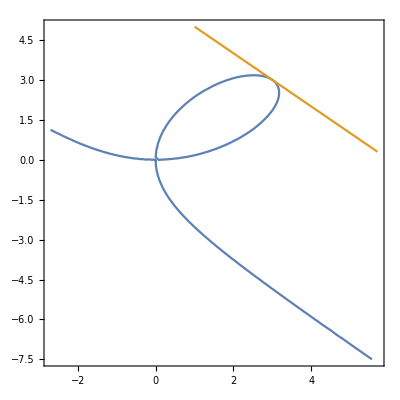

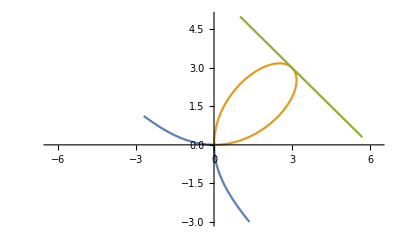

{{Dt[y,x]→(x^2-2 y)/(2 x-y^2)}}

{{y→x^2/2}}

{{x→-1.25992-2.18225 ⅈ,y→-1.5874+2.74946 ⅈ},{x→-1.25992+2.18225 ⅈ,y→-1.5874-2.74946 ⅈ},{x→2.51984,y→3.1748},{x→0.,y→0.},{x→0.,y→0.},{x→0.,y→0.}}

```mathematica
ClearAll[x,y,eq,impdereq,dersol,plot,points,m,tanline]
plot=ContourPlot[{x^3+y^3==6*x*y,y==6-x},{x,-2.7,5.7},{y,-7.5,5}]
points=Cases[Normal@plot,x_Line:>First@x,Infinity];
ListPlot[points,PlotRange->{{-2 Pi,2 Pi},{-3 ,5}},PlotJoined->True]
eq:=x^3+y^3==6*x*y
impdereq:=Dt[eq,x]
dersol=Solve[impdereq,Dt[y,x]]
slope:=dersol[[1,1,2]]
m:=slope /.{x->3,y->3}
tanline:=3+m*(x-3)
Solve[slope==0,y]
NSolve[{x^3+y^3==6*x*y,y==x^2/2},{x,y}]
```

### EXAMPLE 3

#### -Graphics-

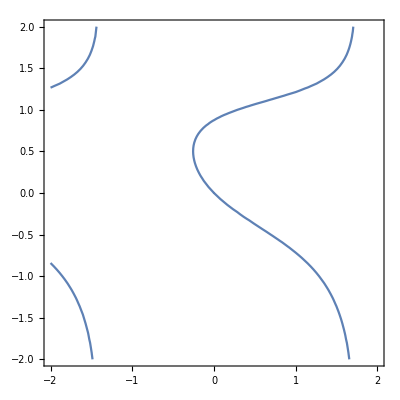

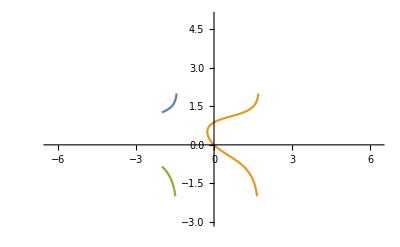

{{Dt[y,x]→(Cos[x+y]+y^2 Sin[x])/(2 y Cos[x]-Cos[x+y])}}

```mathematica
ClearAll[x,y,eq,impdereq,dersol,plot,points,m,tanline]
plot=ContourPlot[{Sin[x+y]==y^2 Cos[x]},{x,-2,2},{y,-2,2}]
points=Cases[Normal@plot,x_Line:>First@x,Infinity];
ListPlot[points,PlotRange->{{-2 Pi,2 Pi},{-3 ,5}},PlotJoined->True]
eq:=Sin[x+y]==y^2 Cos[x]
impdereq:=Dt[eq,x]
dersol=Solve[impdereq,Dt[y,x]]
```

### EXAMPLE 4

#### -Graphics-

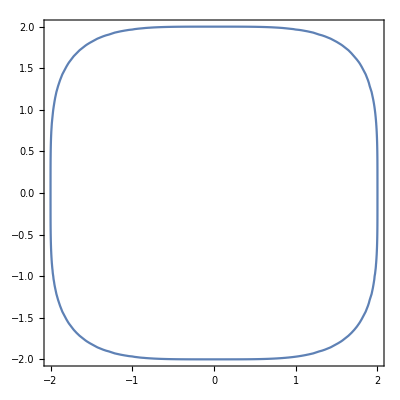

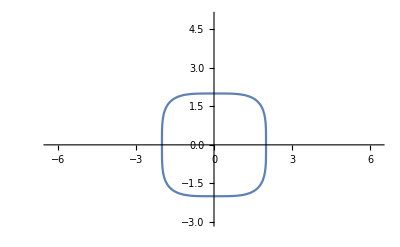

x^4+y^4==16

x^4+y^4==16

4 x^3+4 y^3 Dt[y,x]==0

{{Dt[y,x]→-x^3/y^3}}

-(3 x^2 (x^4+y^4))/y^7

```mathematica
ClearAll[x,y,eq,impdereq,dersol,plot,points]
plot=ContourPlot[x^4+y^4==16,{x,-2,2},{y,-2,2}]
points=Cases[Normal@plot,x_Line:>First@x,Infinity];
ListPlot[points,PlotRange->{{-2 Pi,2 Pi},{-3 ,5}},PlotJoined->True]
eq=x^4+y^4==16
Print[eq]
impdereq:=Dt[eq,x]
Print[impdereq]
dersol:=Solve[impdereq,Dt[y,x]]
Print[dersol]
dersol2:=Dt[-x^3/y^3,x]  /. Dt[y,x]->-x^3/y^3//FullSimplify
Print[dersol2]
```

2.7 RELATED RATES

### EXAMPLE 1

#### -Graphics-

#### -Graphics-

### EXAMPLE 2

#### -Graphics-

#### -Graphics--Graphics-

### EXAMPLE 3

#### -Graphics-

#### -Graphics--Graphics- -Graphics-

### STRATEGY

#### -Graphics-

### EXAMPLE 4

#### -Graphics-

#### -Graphics--Graphics-

### EXAMPLE 5

#### -Graphics-

#### -Graphics--Graphics-

2.8 LINEAR APPROXIMATIONS AND DIFFERENTIALS

## LINEAR APPROXIMATION OR TANGENT LINE APPROXIMATION OF f at a

### INTRODUCTION

#### -Graphics- -Graphics-

### DEFINITION

#### -Graphics-

### EXAMPLE 1

#### -Graphics-

√(3+x)

2

1/(2 √(3+x))

1/4

2+1/4 (-1+x)

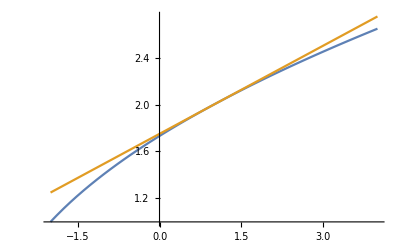

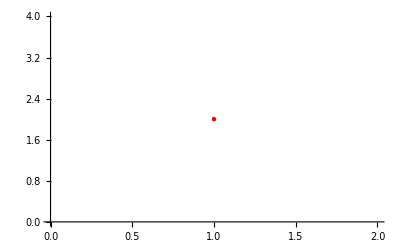

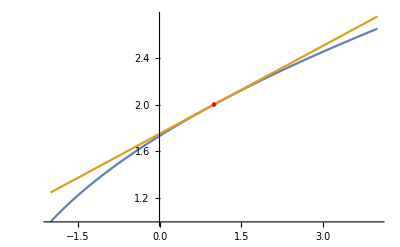

1.99499

1.995

2.01246

2.0125

```mathematica
Clear[f]
Clear[x]
Clear[fprime]
f[x_]=√(x+3)
f[1]
fprime=Dt[f[x],x]
m=fprime /.x->1
l[x_]=2+1/4(x-1)
plot=Plot[{f[x],l[x]},{x,-2,4}]
list=ListPlot[{{1,2}},PlotStyle->{PointSize[Large],Red}]
Show[plot,list]
f[0.98]
l[0.98]
f[1.05]
l[1.05]
```

```mathematica
[3.98]
```

2.01246

ll[4.05]

### EXAMPLE 2

#### -Graphics-

```mathematica
(*NSovle[Abs[√(x+3)-(7/4+x/4)]==0.5,x]*)
Reduce[-0.5<√(x+3)-(7/4+x/4)<0.5,x,Reals]
Reduce[-0.1<√(x+3)-(7/4+x/4)<0.1,x,Reals]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-2.65685<x<8.65685

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-1.12982<x<3.92982

## APPLICATIONS TO PHYSICS

### INTRODUCTION

Linear approximations are often used in physics. In analyzing the consequences of an equation, a physicist sometimes needs to simplify a function by replacing it with its linear approximation. For instance, in deriving a formula for the period of a pendulum, physics textbooks obtain the expression a_T=-gsinθ for tangential acceleration and then replace sinθ by θ with the remark that sinθ is very close to θ if θ is not too large.

```mathematica
Clear[f]
Clear[x]
f[x_]=Sin[x]
fprime=Dt[f[x],x]
m=fprime /.x->0
L[x_]=f[0]+m(x-0)
```

Sin[x]

Cos[x]

1

x

## DIFFERENTIALS

### DEFINITION 3

### EXPLANATION

#### -Graphics--Graphics-

### FORMULA

#### -Graphics- -Graphics-

```mathematica
Clear[f]
Clear[x]
Clear[fprime]
f[x_]=√(x+3)
fprime[x_]=Dt[f[x],x]
dy=dx*fprime[x]/.{x->1,dx->0.05}
f[1+0.05]
f[1]+dy
```

√(3+x)

1/(2 √(3+x))

0.0125

2.01246

2.0125

```mathematica
21^2*Pi*4*0.05
```

277.088

### EXAMPLE 3

#### -Graphics-

```mathematica
Clear[v]
Clear[vprime]

v[r_]=4/3*π*r^3
vprime[r_]=Dt[v[r],r]
dv=vprime[r]*dr /.{ r->21,dr->0.05}
```

(4 π r^3)/3

4 π r^2

277.088